### Full Generality

```mathematica
α = ({{4/9-Sqrt[6]/36}, {4/9+Sqrt[6]/36}, {1/9}});
c0=({{2/5-Sqrt[6]/10}, {2/5+Sqrt[6]/10}, {1}});
c1=({{c11}, {c12}, {c13}});
β1=({{β11}, {β12}, {β13}});
β2=({{β21}, {β22}, {β23}});
A0=({{11/45-(7Sqrt[6])/360, 37/225-(169Sqrt[6])/1800, -2/225+Sqrt[6]/75}, {37/225+(169Sqrt[6])/1800, 11/45+(7Sqrt[6])/360, -2/225-Sqrt[6]/75}, {4/9-Sqrt[6]/36, 4/9+Sqrt[6]/36, 1/9}}); (* A0=({{A011, A012, A013}, {A021, A022, A023}, {A031, A032, A033}}); *)
B0=({{0, 0, 0}, {B021, 0, 0}, {B031, B032, 0}}); (* Subscript[B, 0]=({{B011, B012, B013}, {B021, B022, B023}, {B031, B032, B033}}); *)
H0=({{H01}, {H02}, {H03}});
VU=({{U}, {U}, {U}});
e = ({{1}, {1}, {1}});
```

```mathematica
K1=IdentityMatrix[3] - μ h A0 ;
MatrixForm[K1 ]
```

(1-(11/45-7/(60 √6)) h μ | -(37/225-169/(300 √6)) h μ | -(-2/225+(√(2/3))/25) h μ
-(37/225+169/(300 √6)) h μ | 1-(11/45+7/(60 √6)) h μ | -(-2/225-(√(2/3))/25) h μ
-(4/9-1/(6 √6)) h μ | -(4/9+1/(6 √6)) h μ | 1-(h μ)/9)

```mathematica
K2 = VU + B0 . e  σ (σ I10)/h;
MatrixForm[K2]
```

(U
U+(B021 I10 σ^2)/h
U+((B031+B032) I10 σ^2)/h)

```mathematica
H0= Inverse[K1].K2;
MatrixForm[H0]
```

((U (1-(16 h μ)/45-(7 h μ)/(60 √6)+(h^2 μ^2)/30+4/225 √(2/3) h^2 μ^2+(13 h^2 μ^2)/(900 √6)))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+(((37 h μ)/225-(169 h μ)/(300 √6)-(h^2 μ^2)/50+4/225 √(2/3) h^2 μ^2+(11 h^2 μ^2)/(180 √6)) (U+(B021 I10 σ^2)/h))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+((-(2 h μ)/225+1/25 √(2/3) h μ+(h^2 μ^2)/150-1/75 √(2/3) h^2 μ^2) (U+((B031+B032) I10 σ^2)/h))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)
(U ((37 h μ)/225+(169 h μ)/(300 √6)-(h^2 μ^2)/50-4/225 √(2/3) h^2 μ^2-(11 h^2 μ^2)/(180 √6)))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+((1-(16 h μ)/45+(7 h μ)/(60 √6)+(h^2 μ^2)/30-4/225 √(2/3) h^2 μ^2-(13 h^2 μ^2)/(900 √6)) (U+(B021 I10 σ^2)/h))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+((-(2 h μ)/225-1/25 √(2/3) h μ+(h^2 μ^2)/150+1/75 √(2/3) h^2 μ^2) (U+((B031+B032) I10 σ^2)/h))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)
(U ((4 h μ)/9-(h μ)/(6 √6)-(h^2 μ^2)/60+2/15 √(2/3) h^2 μ^2))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+(((4 h μ)/9+(h μ)/(6 √6)-(h^2 μ^2)/60-2/15 √(2/3) h^2 μ^2) (U+(B021 I10 σ^2)/h))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+((1-(22 h μ)/45+(h^2 μ^2)/12) (U+((B031+B032) I10 σ^2)/h))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60))

```mathematica
U2= U+ μ h αᵀ.H0 + σ I1 Transpose[e].β1+ σ I10/h Transpose[e].β2;
U2 =U2[[1]][[1]];
U2
```

U+I1 (β11+β12+β13) σ+(I10 (β21+β22+β23) σ)/h+h μ (1/9 ((U ((4 h μ)/9-(h μ)/(6 √6)-(h^2 μ^2)/60+2/15 √(2/3) h^2 μ^2))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+(((4 h μ)/9+(h μ)/(6 √6)-(h^2 μ^2)/60-2/15 √(2/3) h^2 μ^2) (U+(B021 I10 σ^2)/h))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+((1-(22 h μ)/45+(h^2 μ^2)/12) (U+((B031+B032) I10 σ^2)/h))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60))+(4/9-1/(6 √6)) ((U (1-(16 h μ)/45-(7 h μ)/(60 √6)+(h^2 μ^2)/30+4/225 √(2/3) h^2 μ^2+(13 h^2 μ^2)/(900 √6)))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+(((37 h μ)/225-(169 h μ)/(300 √6)-(h^2 μ^2)/50+4/225 √(2/3) h^2 μ^2+(11 h^2 μ^2)/(180 √6)) (U+(B021 I10 σ^2)/h))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+((-(2 h μ)/225+1/25 √(2/3) h μ+(h^2 μ^2)/150-1/75 √(2/3) h^2 μ^2) (U+((B031+B032) I10 σ^2)/h))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60))+(4/9+1/(6 √6)) ((U ((37 h μ)/225+(169 h μ)/(300 √6)-(h^2 μ^2)/50-4/225 √(2/3) h^2 μ^2-(11 h^2 μ^2)/(180 √6)))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+((1-(16 h μ)/45+(7 h μ)/(60 √6)+(h^2 μ^2)/30-4/225 √(2/3) h^2 μ^2-(13 h^2 μ^2)/(900 √6)) (U+(B021 I10 σ^2)/h))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+((-(2 h μ)/225-1/25 √(2/3) h μ+(h^2 μ^2)/150+1/75 √(2/3) h^2 μ^2) (U+((B031+B032) I10 σ^2)/h))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)))

```mathematica
I10=1/2 h(W+Z/(√3)); 
I1= W;
```

```mathematica
U2Full = U2
```

U+W (β11+β12+β13) σ+1/2 (W+Z/(√3)) (β21+β22+β23) σ+h μ (1/9 ((U ((4 h μ)/9-(h μ)/(6 √6)-(h^2 μ^2)/60+2/15 √(2/3) h^2 μ^2))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+(((4 h μ)/9+(h μ)/(6 √6)-(h^2 μ^2)/60-2/15 √(2/3) h^2 μ^2) (U+1/2 B021 (W+Z/(√3)) σ^2))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+((1-(22 h μ)/45+(h^2 μ^2)/12) (U+1/2 (B031+B032) (W+Z/(√3)) σ^2))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60))+(4/9-1/(6 √6)) ((U (1-(16 h μ)/45-(7 h μ)/(60 √6)+(h^2 μ^2)/30+4/225 √(2/3) h^2 μ^2+(13 h^2 μ^2)/(900 √6)))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+(((37 h μ)/225-(169 h μ)/(300 √6)-(h^2 μ^2)/50+4/225 √(2/3) h^2 μ^2+(11 h^2 μ^2)/(180 √6)) (U+1/2 B021 (W+Z/(√3)) σ^2))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+((-(2 h μ)/225+1/25 √(2/3) h μ+(h^2 μ^2)/150-1/75 √(2/3) h^2 μ^2) (U+1/2 (B031+B032) (W+Z/(√3)) σ^2))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60))+(4/9+1/(6 √6)) ((U ((37 h μ)/225+(169 h μ)/(300 √6)-(h^2 μ^2)/50-4/225 √(2/3) h^2 μ^2-(11 h^2 μ^2)/(180 √6)))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+((1-(16 h μ)/45+(7 h μ)/(60 √6)+(h^2 μ^2)/30-4/225 √(2/3) h^2 μ^2-(13 h^2 μ^2)/(900 √6)) (U+1/2 B021 (W+Z/(√3)) σ^2))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+((-(2 h μ)/225-1/25 √(2/3) h μ+(h^2 μ^2)/150+1/75 √(2/3) h^2 μ^2) (U+1/2 (B031+B032) (W+Z/(√3)) σ^2))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)))

```mathematica
U2Plugged = U2Full /.  {W -> 0,Z->0}
G = Coefficient[U2Plugged,U]
```

U+h μ (1/9 ((U (1-(22 h μ)/45+(h^2 μ^2)/12))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+(U ((4 h μ)/9+(h μ)/(6 √6)-(h^2 μ^2)/60-2/15 √(2/3) h^2 μ^2))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+(U ((4 h μ)/9-(h μ)/(6 √6)-(h^2 μ^2)/60+2/15 √(2/3) h^2 μ^2))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60))+(4/9+1/(6 √6)) ((U (-(2 h μ)/225-1/25 √(2/3) h μ+(h^2 μ^2)/150+1/75 √(2/3) h^2 μ^2))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+(U ((37 h μ)/225+(169 h μ)/(300 √6)-(h^2 μ^2)/50-4/225 √(2/3) h^2 μ^2-(11 h^2 μ^2)/(180 √6)))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+(U (1-(16 h μ)/45+(7 h μ)/(60 √6)+(h^2 μ^2)/30-4/225 √(2/3) h^2 μ^2-(13 h^2 μ^2)/(900 √6)))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60))+(4/9-1/(6 √6)) ((U (-(2 h μ)/225+1/25 √(2/3) h μ+(h^2 μ^2)/150-1/75 √(2/3) h^2 μ^2))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+(U (1-(16 h μ)/45-(7 h μ)/(60 √6)+(h^2 μ^2)/30+4/225 √(2/3) h^2 μ^2+(13 h^2 μ^2)/(900 √6)))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)+(U ((37 h μ)/225-(169 h μ)/(300 √6)-(h^2 μ^2)/50+4/225 √(2/3) h^2 μ^2+(11 h^2 μ^2)/(180 √6)))/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)))

1+(h μ)/(1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60)-(h^2 μ^2)/(10 (1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60))+(h^3 μ^3)/(60 (1-(3 h μ)/5+(3 h^2 μ^2)/20-(h^3 μ^3)/60))

```mathematica
stableeq = FullSimplify[G/.  {μ -> z/h}]
```

-(3 (20+z (8+z)))/(-60+z (36+(-9+z) z))

```mathematica
GG[z_]:=(2 (3+2 √2+z+√2 z))/(2+√2-z)^2
```

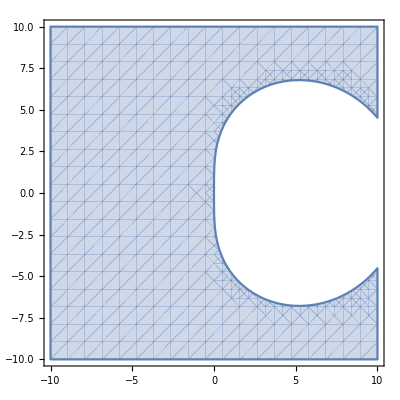

```mathematica
RegionPlot[Abs[GG[x+ⅈ y]]<1,{x,-10,10},{y,-10,10}]
```

```mathematica
cond1 = First[First[Transpose[α].e]] == 1;
cond2 = First[First[Transpose[β1].e]] == 1;
cond3 = First[First[Transpose[β2].e]] == 0;
cond4 = First[First[Transpose[α].B0.e]] == 1;
cond5 = First[First[Transpose[α].A0.e]] == 1/2;
cond6 = First[First[Transpose[α].(B0.e)^2]] == 3/2;
cond7 = First[First[Transpose[β1].c1]] == 1;
cond8 = First[First[Transpose[β2].c1]] == -1;
```

```mathematica
conds = {cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8}
vars = {β11,β12,β13,β21,β22,β23,B021,B031,B032,c11,c12,c13};
```

{True,β11+β12+β13==1,β21+β22+β23==0,(4/9+1/(6 √6)) B021+B031/9+B032/9==1,True,(4/9+1/(6 √6)) B021^2+1/9 (B031+B032)^2==3/2,c11 β11+c12 β12+c13 β13==1,c11 β21+c12 β22+c13 β23==-1}

```mathematica
FindInstance[conds ,vars,Reals]
```

{}